```mathematica
Formula1 = 2x + 2y + z;
Formula2 = x^2 + 5y + 2z;
Formula3 = x + y + z;
answer = Solve[{Formula1 == 2, Formula2 == 5, Formula3 == 2}, {x, y, z}]
```

{{x→1/2 (5-√29),y→1/2 (-5+√29),z→2},{x→1/2 (5+√29),y→1/2 (-5-√29),z→2}}

```mathematica
Solve[x^2 == -1, x]
```

{{x→-ⅈ},{x→ⅈ}}

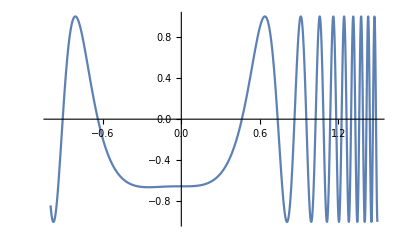

{x→-0.638054}

```mathematica
Formula4 = Cos[9x^4 + 3x^3 + 4];
{xL, xR} = {-1, 1.5};
Plot[Formula4, {x, xL, xR}]
Sol = FindRoot[Formula4 == 0, {x, -0.65}]
```

```mathematica
Guess = {1, 3, 5};
Arr = {};
Do[
temp = Guess[[k]];
temp = 2k + k;
Arr = Append[Arr, temp],
{k, 1, 3}];
Arr
```

{3,6,9}

```mathematica
GCD@@{3,6,9}
```

3

```mathematica
PrimePi[3]
```

2

```mathematica
DivisorSigma[1,2]==2 2
```

False

{-120,120}

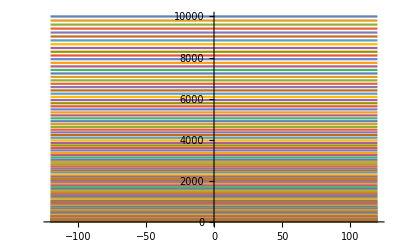

```mathematica
a = Table[x^2, {x, -100, 10, 1}];
{xL, xR} = {-120, 120}
Plot[a, {x, xL, xR}]
```

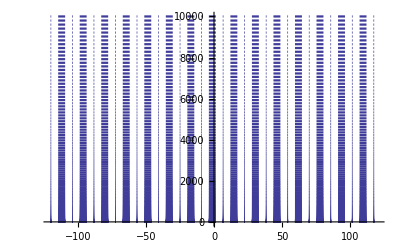

```mathematica
Plot[a,{x,xL,xR},PlotStyle->Directive[Hue[0.6699931334401464,0.6,0.6],DotDashed]]
```

```mathematica
%87
```

{10000,9801,9604,9409,9216,9025,8836,8649,8464,8281,8100,7921,7744,7569,7396,7225,7056,6889,6724,6561,6400,6241,6084,5929,5776,5625,5476,5329,5184,5041,4900,4761,4624,4489,4356,4225,4096,3969,3844,3721,3600,3481,3364,3249,3136,3025,2916,2809,2704,2601,2500,2401,2304,2209,2116,2025,1936,1849,1764,1681,1600,1521,1444,1369,1296,1225,1156,1089,1024,961,900,841,784,729,676,625,576,529,484,441,400,361,324,289,256,225,196,169,144,121,100,81,64,49,36,25,16,9,4,1,0,1,4,9,16,25,36,49,64,81,100}